Layout and Display

Earlier we saw how to use Framed to add a frame when one displays something.

Generate a number and put a frame around it:

```mathematica
Framed[2^100]
```

1267650600228229401496703205376

You can give options to Framed.

Specify a background color and a frame style:

```mathematica
Framed[2^100,Background->LightYellow,FrameStyle->LightGray]
```

1267650600228229401496703205376

Labeled lets you make things be labeled.

Add a label to the framed number:

```mathematica
Labeled[Framed[2^100],"a big number"]
```

1267650600228229401496703205376a big number

This adds a label to a number styled with a yellow background:

```mathematica
Labeled[Style[2^100,Background->Yellow],"a big number"]
```

1267650600228229401496703205376a big number

This adds styling to the label:

```mathematica
Labeled[Style[2^100,Background->Yellow],Style["a big number",Italic,Orange]]
```

1267650600228229401496703205376a big number

You can use Labeled in graphics as well.

Make a pie chart in which some wedges are labeled:

```mathematica
PieChart[{Labeled[1,"one"],Labeled[2,"two"],Labeled[3,Red],Labeled[4,Orange],2,2}]
```

-Graphics-

Plot labeled points:

```mathematica
ListPlot[{Labeled[1,"one"],Labeled[2,"two"],Labeled[3,Pink],Labeled[4,Yellow],5,6,7}]
```

-Graphics-

Plot the first few primes labeled with their values:

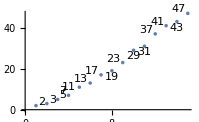

```mathematica
ListPlot[Table[Labeled[Prime[n],Prime[n]],{n,15}]]
```

Labeled indicates something by putting a label right next to it. It’s often nice instead to use “callouts”, that have little lines pointing to whatever they’re referring to. You can do this by using Callout rather than Labeled.

Callout creates “callouts” with little lines:

```mathematica
ListPlot[Table[Callout[Prime[n],Prime[n]],{n,15}]]
```

-Graphics-

There are all sorts of ways to annotate graphics. Style directly inserts styling. Tooltip generates interactive tooltips that show themselves when the mouse hovers over them. Legended puts labels into a legend on the side.

Specify styles for the first three pie wedges:

```mathematica
PieChart[{Style[3,Red],Style[2,Green],Style[1,Yellow],1,2}]
```

-Graphics-

Set up words and colors as legends for pie wedges:

```mathematica
PieChart[{Legended[1,"one"],Legended[2,"two"],Legended[3,Pink],Legended[4,Yellow],2,2}]
```

-Graphics-

The default plot theme for the web is more brightly colored:

```mathematica
PieChart[{1,2,3,4,2,2},PlotTheme->"Web"]
```

-Graphics-

If you want the Wolfram Language to just automatically pick how to annotate things, then simply give the annotations with rules (→).

In ListPlot, annotations specified by rules are implemented with callouts:

```mathematica
ListPlot[{1->"one",2->"two",3->Pink,4->Yellow,5,6,7}]
```

-Graphics-

In PieChart, strings are assumed to be labels, and colors to be styles:

```mathematica
PieChart[{1->"one",2->"two",3->Blue,4->Red}]
```

-Graphics-

It’s common to want to combine different objects for presentation. Row, Column and Grid are convenient ways to do this.

Display a list of objects in a row:

```mathematica
Row[{Yellow,Pink,Cyan}]
```

RGBColor[1, 1, 0]RGBColor[1, 0.5, 0.5]RGBColor[0, 1, 1]

Display objects in a column:

```mathematica
Column[{Yellow,Pink,Cyan}]
```

RGBColor[1, 1, 0]
RGBColor[1, 0.5, 0.5]
RGBColor[0, 1, 1]

Use GraphicsRow, GraphicsColumn and GraphicsGrid to arrange objects to fit in a certain overall size.

Generate an array of random pie charts, sized to fit:

```mathematica
GraphicsGrid[Table[PieChart[RandomReal[10,5]],3,6]]
```

-Graphics-

Do it with a frame around everything:

```mathematica
GraphicsGrid[Table[PieChart[RandomReal[10,5]],3,6],Frame->All]
```

-Graphics-

Vocabulary

Framed[expr] |   | add a frame 
Labeled[expr,lab] |   | add a label 
Callout[expr,lab] |   | add a callout
Tooltip[expr,lab] |   | add an interactive tooltip 
Legended[expr,lab] |   | add a legend 
Row[{expr_1,expr_2, ...}] |   | arrange in a row 
Column[{expr_1,expr_2, ...}] |   | arrange in a column 
GraphicsRow[{expr_1,expr_2, ...}] |   | arrange in a resizable row 
GraphicsColumn[{expr_1,expr_2, ...}] |   | arrange in a resizable column 
GraphicsGrid[array] |   | arrange in a resizable grid

"8 Exercises Available" | "Get Started »"

Make a list of numbers up to 100, with even numbers on yellow and odd numbers on light gray. »

| Expected output: |  
  | {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100} |

Make a list of numbers up to 100, with primes framed. »

| Expected output: |  
  | {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100} |

Make a list of numbers up to 100, with primes framed and labeled in light gray with their values modulo 4. »

| Expected output: |  
  | {1,22,33,4,51,6,73,8,9,10,113,12,131,14,15,16,171,18,193,20,21,22,233,24,25,26,27,28,291,30,313,32,33,34,35,36,371,38,39,40,411,42,433,44,45,46,473,48,49,50,51,52,531,54,55,56,57,58,593,60,611,62,63,64,65,66,673,68,69,70,713,72,731,74,75,76,77,78,793,80,81,82,833,84,85,86,87,88,891,90,91,92,93,94,95,96,971,98,99,100} |

Create a 3×6 GraphicsGrid of randomly colored disks. »

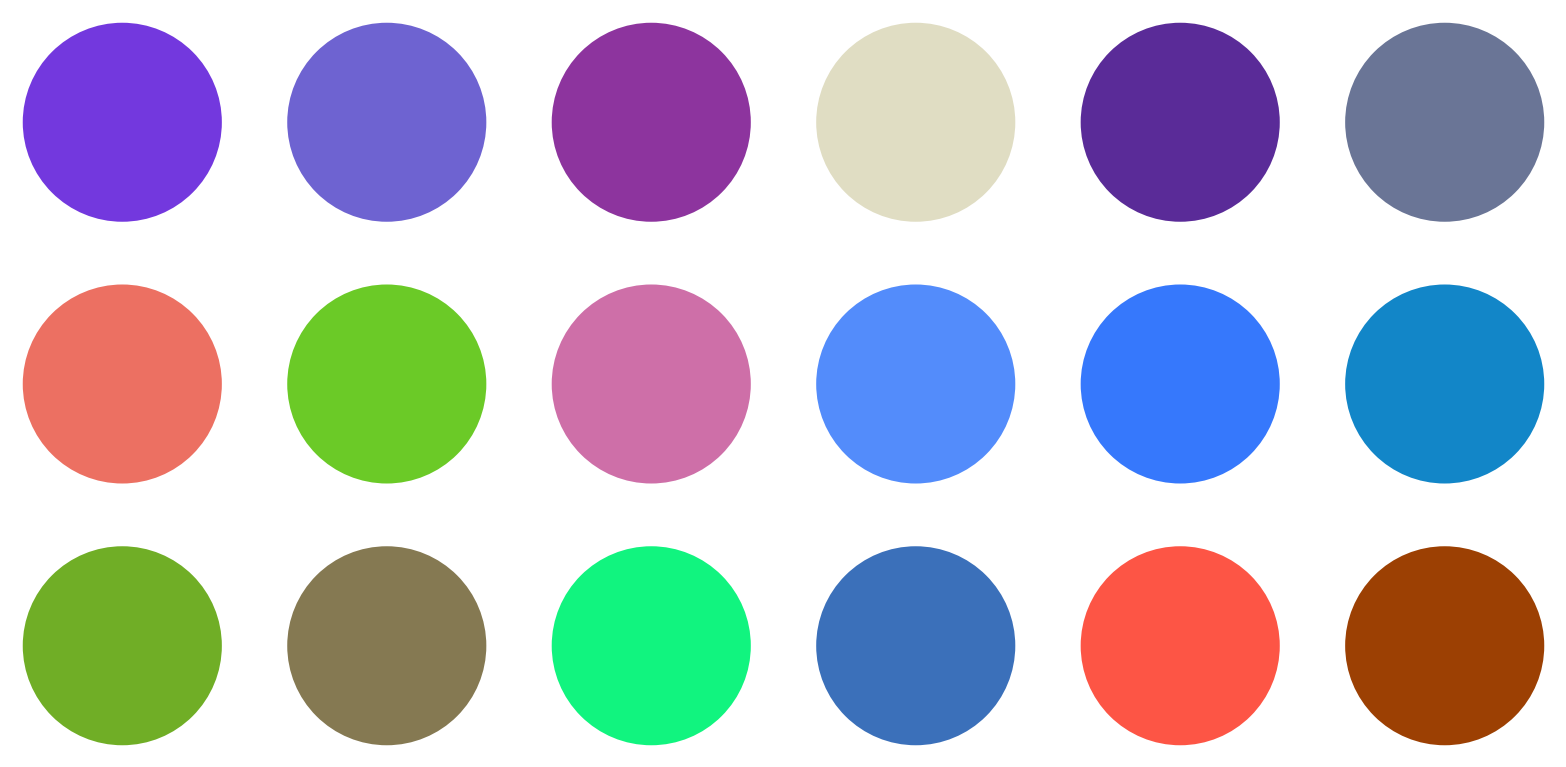
| Sample expected output: |  
  | -Graphics- |

Make a pie chart of the GDPs of the countries in the G5, labeling each wedge. »

| Sample expected output: |  
  | -Graphics- |

Make a pie chart of the populations of the countries in the G5, giving a legend for each wedge. »

| Sample expected output: |  
  | -Graphics- |

Make a 5×5 GraphicsGrid of pie charts that give the relative frequencies of digits in 2^n with n starting at 1. »

| Expected output: |  
  | -Graphics- |

Make a graphics row of word clouds for Wikipedia articles on the G5 countries. »

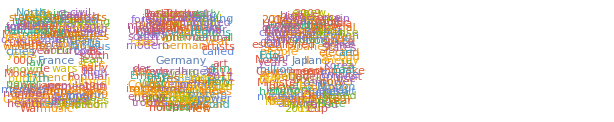
| Sample expected output: |  
  | -Graphics- |

Q&A

Can I get rounded corners with Framed?

Yes. Use an option like RoundingRadius→0.2.

What kinds of things can be in a label?

Anything you want. A label can be text or a graphic or, for that matter, a whole notebook.

Can I use Labeled to put labels in places other than at the bottom?

Yes. Use e.g. Labeled[expr,label,Left] or Labeled[expr,label,Right].

How do I determine where a legend goes?

Use Placed.

Can visualization be animated or dynamic?

Yes. ListAnimate creates an animation. Constructs from Tooltip to Manipulate can be used to set up dynamic visualizations.

Tech Notes

The Wolfram Language tries to place labels where they won’t interfere with the data that’s being plotted.

You can resize any graphic using Show[graphic,ImageSize→width] or Show[graphic,ImageSize→{width,height}]. ImageSize→Tiny, etc. also work.

PlotTheme→"BlackBackground" may be useful for people with low vision. PlotTheme→"Monochrome" avoids using color.

ListPlot, PieChart, etc. automatically work with associations (<|...|>), taking keys to be coordinates when appropriate, but otherwise treating them as annotations.

There are lots of different kinds of legends: LineLegend, BarLegend, etc.

More to Explore

Guide to Labeling & Annotation in the Wolfram Language »